```mathematica
<< MaTeX`
```

## Первый график

```mathematica
Θ = 1;
Δ = 2Θ ⅇ^(-1/0.43);
Print[Θ/Δ];
ClearAll[v];
v[ξ_] := 1/2(1-(Δ ξ)/(√(Δ^2+ ξ^2 Δ^2)));
```

5.11631

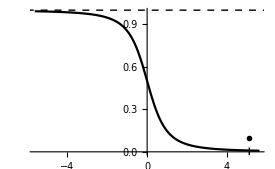

```mathematica
img1 = Plot[v[ξ], {ξ,-1.1 Θ/Δ ,1.1 Θ/Δ}, PlotStyle->Black,Epilog->
{
{Dashed, Black, Line[{{-2 Θ/Δ, 1}, {2 Θ/Δ, 1}}]},
{Text[MaTeX@"\\Theta_D", {Θ/Δ, 0.1}]},
{Black, Line[{{ Θ/Δ, -0.03}, {Θ/Δ, 0.03}}]}
},
AxesLabel->{MaTeX@"\\xi_{\\boldsymbol{k}}, \\Delta", MaTeX@"|v_{\\boldsymbol{k}}|^2"},
ImageSize->1.1{250, 150}
]
```

```mathematica
Export[NotebookDirectory[]<>"plot_1.pdf", img1]
```

D:\git\notes_6sem\physics\cq\plot_1.pdf

## Второй график

```mathematica
Δ
```

0.195453

```mathematica
Δ/1.76
```

0.111053

```mathematica
ClearAll[Tint];
Tint[T_, Δ_] := NIntegrate[Tanh[(√(ξ^2+δ^2))/(2 T)]/(√(ξ^2+δ^2))-1/0.43 /. {δ->Δ},{ξ,0, Θ}];
```

```mathematica
step = 10.^-2;
δs = Δ Range[step, 1, step];
Ts = ParallelTable[
T/. Quiet@FindRoot[Tint[T, α Δ], {T, 0.05}]
,{α,step, 1, step}];
```

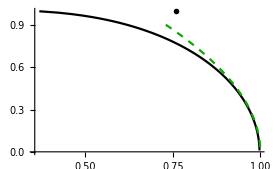

```mathematica
green = RGBColor[0.06,0.66,0.];
img2 = Show[{
ListLinePlot[Transpose@{Ts/(Δ/1.76), δs/Δ}, PlotStyle->Black, PlotRange->{Automatic, {0, Full}}, AxesLabel->{
MaTeX@"T/T_{c}",
MaTeX@"\\Delta(T)/\\Delta(0)"
}, ImageSize->1.1{250, 150}, Epilog->{Text[MaTeX@"1.74 \\sqrt{1-T/T_c}", {0.76, 1}]}],
Plot[1.74 √(1-T), {T,0.73, 1}, PlotStyle->{green, Dashed}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"plot_2.pdf", img2]
```

D:\git\notes_6sem\physics\cq\plot_2.pdf